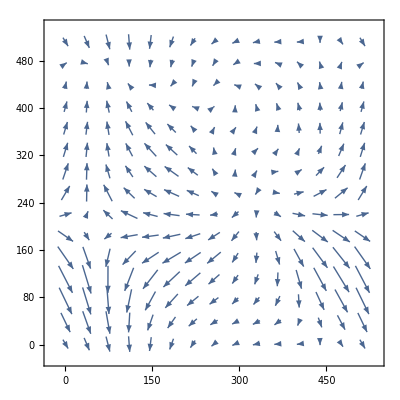

DiscreteWaveletData[<<DWT>>, <3>, {512, 512}]

DiscreteWaveletData[<<DWT>>, <3>, {512, 512}]

List

-Graphics-

```mathematica
v=Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\velocity.txt","Table"];
u=Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\uelocity.txt","Table"];
t = Import["D:\\YanXiao\\Github\\Divergence-free_Wavelet\\mathematica\\t.txt","Table"];
ListVectorPlot[Table[{u[[x,y]],v[[x,y]]},{x,512},{y,512}]]
dwdu = DiscreteWaveletTransform[u,ReverseBiorthogonalSplineWavelet[1,3],3]
dwdv = DiscreteWaveletTransform[u,ReverseBiorthogonalSplineWavelet[1,3],3]
Normal[dwdv][[0]]
```

```mathematica
Plot3D[u, {u, -1, 1}, {x, -1, 1}]
```

-Graphics3D-

```mathematica
v
```

{{-0.001247,-0.001249,-0.00125,-0.001251,-0.001251,-0.001252,-0.001252,-0.001253,-0.001253,-0.001253,-0.001253,-0.001253,-0.001253,-0.001252,484,-0.001224,-0.001226,-0.001228,-0.00123,-0.001232,-0.001234,-0.001235,-0.001237,-0.001239,-0.00124,-0.001242,-0.001243,-0.001245,-0.001246},511}
 |  |  |  |